# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2023 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Anli-Gungor phase function

```mathematica
Clear[pAG];pAG[u_,t_]:=1/(4 Pi)1/(√(1+t^2-2 t u))
```

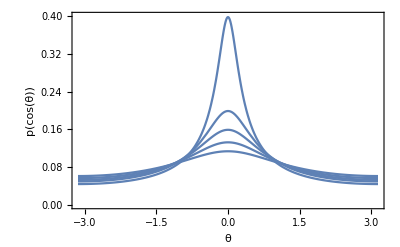

```mathematica
pHGplot=Show[
Plot[pAG[Cos[t],.8],{t,-Pi,Pi},PlotRange->{0,.4}],
Plot[pAG[Cos[t],.6],{t,-Pi,Pi},PlotRange->All],
Plot[pAG[Cos[t],.5],{t,-Pi,Pi},PlotRange->All],
Plot[pAG[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pAG[Cos[t],.3],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Anli-Gungor Scattering, t = 0.3, 0.4, 0.5, 0.6, 0.8"}}]
```

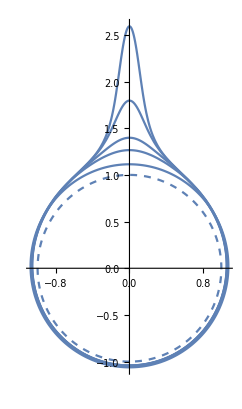

```mathematica
Show[
ParametricPlot[{Sin[t],Cos[t]}(1),{t,-Pi,Pi},PlotRange->All,PlotStyle->Dashed],
ParametricPlot[{Sin[t],Cos[t]}(1+pAG[Cos[t],0.95]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pAG[Cos[t],0.9]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pAG[Cos[t],0.8]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pAG[Cos[t],0.7]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pAG[Cos[t],0.3]),{t,-Pi,Pi},PlotRange->All]
]
```

### Normalization condition

```mathematica
Integrate[2 Pi pAG[u,t],{u,-1,1},Assumptions->-1<t<1]
```

1

### Mean Cosine

```mathematica
Integrate[2 Pi pAG[u,t]u,{u,-1,1},Assumptions->-1<t<1]
```

t/3

### Back-scattering fraction

```mathematica
FullSimplify[Integrate[2 Pi pAG[u,t],{u,-1,0},Assumptions->t>-1&&t<1],Assumptions->-1<g<1]
```

1/(1+t+√(1+t^2))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pAG[u,t]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->t>-1&&t<1]
```

1

```mathematica
Integrate[2Pi(2k+1)pAG[u,t]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->t>-1&&t<1]
```

t

```mathematica
Integrate[2Pi(2k+1)pAG[u,t]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->t>-1&&t<1]
```

t^2

```mathematica
Integrate[2Pi(2k+1)pAG[u,t]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->t>-1&&t<1]
```

t^3

### Legendre Approximations

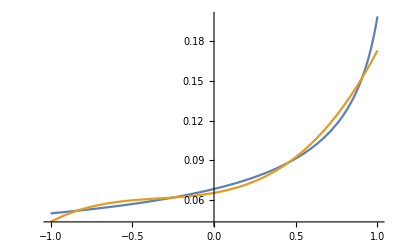

```mathematica
With[{t=0.6},
Plot[{pAG[u,t],1/(4Pi)Sum[t^k LegendreP[k,u],{k,0,3}]},{u,-1,1},PlotRange->All]
]
```

### sampling

```mathematica
cdf=Integrate[2 Pi pAG[u,t],{u,-1,x},Assumptions->t>-1&&t<1&&x<1]
```

(1+t-√(1+t^2-2 t x))/(2 t)

```mathematica
Solve[cdf==e,x]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→-1+2 e+2 e t-2 e^2 t}}

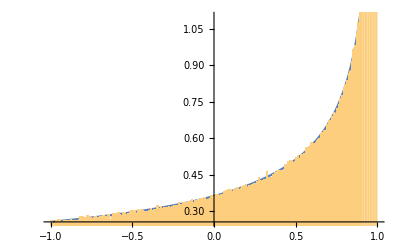

```mathematica
t=0.95;
Show[
Plot[2 Pi pAG[u,t],{u,-1,1}],
Histogram[Map[-1+2 #+2# t-2 #^2 t&,Table[RandomReal[],{i,1,1000000}]],150,"PDF"]
]
Clear[t];
```